## DEFINING FUNCTIONS

```mathematica
takeNetwork[file_]:=Module[{},
data=Import[file,"table"];
connections=Transpose[Transpose[data[[(2+data[[1]][[1]]+data[[1]][[2]]);;(1+data[[1]][[1]]+data[[1]][[2]]+data[[1]][[3]])]]][[1;;2]]];
getLineCoordinates[x_]:=Module[{},Line[{data[[1+x[[1]]]][[1;;2]],data[[1+x[[2]]]][[1;;2]]}]];
Map[getLineCoordinates,connections]
]

takeMesh[file_]:=Module[{},
data=Import[file,"table"];
connections=Transpose[Transpose[data[[(2+data[[1]][[1]]);;(1+data[[1]][[1]]+data[[1]][[2]])]]][[1;;3]]];
getLineCoordinates[x_]:=Module[{},Line[{data[[1+x[[1]]]][[1;;2]],data[[1+x[[2]]]][[1;;2]],data[[1+x[[3]]]][[1;;2]],data[[1+x[[1]]]][[1;;2]]}]];
Map[getLineCoordinates,connections]
]

takeTriangles[file_]:=Module[{},
data=Import[file,"table"];
connections=Transpose[Transpose[data[[(2+data[[1]][[1]]);;(1+data[[1]][[1]]+data[[1]][[2]])]]][[1;;3]]];
getLineCoordinates[x_]:=Module[{},Triangle[{data[[1+x[[1]]]][[1;;2]],data[[1+x[[2]]]][[1;;2]],data[[1+x[[3]]]][[1;;2]]}]];
Map[getLineCoordinates,connections]
]

takePoints[file_]:=Module[{},
data=Import[file,"table"];
connections=Transpose[Transpose[data[[(2+data[[1]][[1]]);;(1+data[[1]][[1]]+data[[1]][[2]])]]][[1;;3]]]
]

takeCoords[file_]:=Module[{},
data=Import[file,"table"];
connections=Transpose[Transpose[data[[(2+data[[1]][[1]]);;(1+data[[1]][[1]]+data[[1]][[2]])]]][[1;;3]]];
getLineCoordinates[x_]:=Module[{},{data[[1+x[[1]]]][[1;;2]],data[[1+x[[2]]]][[1;;2]],data[[1+x[[3]]]][[1;;2]],data[[1+x[[1]]]][[1;;2]]}];
Map[getLineCoordinates,connections]
]

takeAngles[file]:=Module[{},
connections=takeCoords[file];

Angle[x_]:=Module[{},{N[VectorAngle[x[[1]]-x[[2]],x[[3]]-x[[2]]]/Degree],
N[VectorAngle[x[[2]]-x[[3]],x[[4]]-x[[3]]]/Degree],
N[VectorAngle[x[[3]]-x[[1]],x[[2]]-x[[1]]]/Degree]}];
Map[Angle,connections]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
file1="Mesh.msh";
data=Import[file1,"table"];
drawNetwork=takeNetwork[file1];
drawMesh=takeMesh[file1];
drawTriangles=takeTriangles[file1];
Points=takePoints[file1];
Coords=takeCoords[file1];
Angles=takeAngles[file1];
Areas=Map[Area,drawTriangles];
```

```mathematica
data
```

{{4525,8414,637},{-1,0,0},{0,0,0},{1,0,0},{1,50,0},{-1,50,0},{0,0.5,0},{-0.00587785,0.50809,0},{0.0176336,0.524271,0},{-0.928571,0,0},{-0.857143,0,0},{-0.785714,0,0},{-0.714286,0,0},{-0.642857,0,0},{-0.571429,0,0},{-0.5,0,0},{-0.428571,0,0},{-0.357143,0,0},{-0.285714,0,0},{-0.214286,0,0},{-0.142857,0,0},{-0.0714286,0,0},{0.0714286,0,0},{0.142857,0,0},{0.214286,0,0},{0.285714,0,0},{0.357143,0,0},{0.428571,0,0},{0.5,0,0},{0.571429,0,0},{0.642857,0,0},{0.714286,0,0},{0.785714,0,0},{0.857143,0,0},13510,{605,606,2},{606,607,2},{607,608,2},{608,609,2},{609,610,2},{610,611,2},{611,612,2},{612,613,2},{613,614,2},{614,615,2},{615,616,2},{616,617,2},{617,618,2},{618,619,2},{619,620,2},{620,621,2},{621,622,2},{622,623,2},{623,624,2},{624,625,2},{625,626,2},{626,627,2},{627,628,2},{628,629,2},{629,630,2},{630,631,2},{631,632,2},{632,633,2},{633,634,2},{634,635,2},{635,636,2},{636,637,2},{637,1,2}}
 |  |  |  |

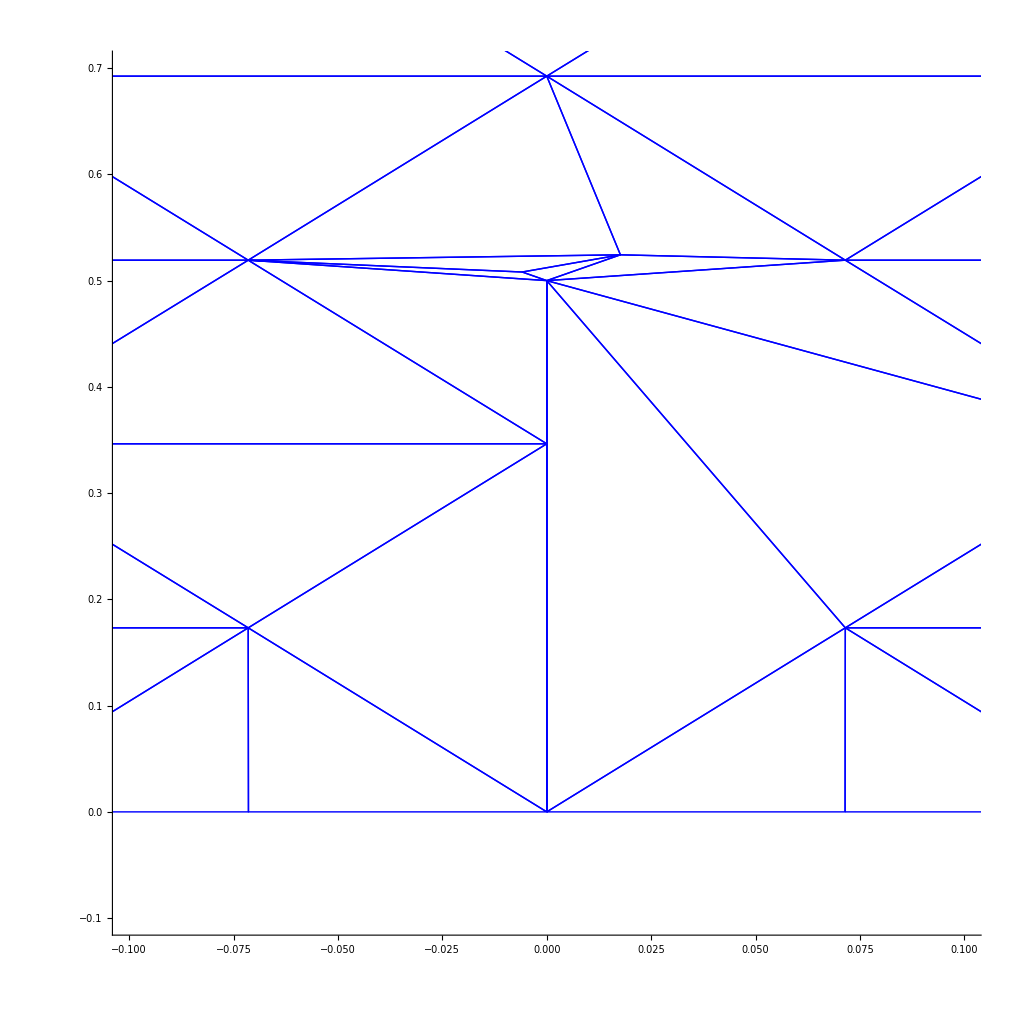

```mathematica
w1=Graphics[{Blue, Thickness[0.001],drawMesh},AspectRatio->1,PlotRange->{{-0.1,0.1},{-0.1,0.7}},Axes->True,AxesOrigin->{-1,0}]
(* w2=Graphics[{Blue,drawMesh2,Red,Thickness[0.001],drawNetwork2},PlotRange->{{-1.1,1.1},{-0.1,50}},AspectRatio->2,ImageSize->200]*)
```

## IMPORTING AND PROCESSING DATA

```mathematica
Table[n,{n,1,15}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
folder1="initialLength5v3/";
folder2="initialLength5/mesh/";
folder3="bifurcatedTip/";
filesNames=Flatten[Table[{folder1<>"lap"<>ToString[n]<>"_boundary.msh"},{n,1,15}]];
SetDirectory[NotebookDirectory[]];
data=Import[#,"table"]&/@filesNames;
(*threeLap = Import[#,"table"]&/@Table["lap"<>ToString[n]<>".msh",{n,{5,10,15}}];*)
Length@data
```

15

```mathematica
points = pointsFromMesh/@Range[15];
Do[points[[i]][[All,1]]+=-1,{i,1,15}];
```

## VISUALISING MESH

### Graphics row

```mathematica
pr={{0,2},{0,6}};
ar=2;
ps=0.015;
subtract=0;
plotGraph[eta_]:=ListPlot[{pointsFromMesh[eta]},PlotStyle->{PointSize->ps},ImageSize->500,PlotRange->pr,AspectRatio->ar,AxesOrigin->{0,0}];
(*pointsFromMesh[i_]:=data[[i]][[2;;data[[i]][[1]][[1]],1;;2]];*)
pointsFromMesh[i_]:=data[[i]][[6;;data[[i]][[5]][[1]]]][[All,2;;3]];
```

```mathematica
Table[n,{n,1,graphsInRow}]
```

{1,2,3,4,5}

```mathematica
graphsInRow=5;
GraphicsGrid[{{GraphicsRow[plotGraph/@Table[1,graphsInRow]]},{GraphicsRow[plotGraph/@Table[n,{n,graphsInRow+1,2graphsInRow}]]},{GraphicsRow[plotGraph/@Table[n,{n,2graphsInRow+1,3graphsInRow}]]}}]
```

-Graphics-

### Comparison

```mathematica
pr={{-1,1},{0,6}};
ar=2;
ps=0.015;
is=1200;
graphsOnPlot=3;
add=5;
filesNames;
comparison=GraphicsRow[{ListPlot[points[[Range@graphsOnPlot]],PlotStyle->{PointSize->ps},ImageSize->is,PlotRange->pr,AspectRatio->ar,AxesOrigin->{-1,0}],
ListPlot[points[[Range[graphsOnPlot+1,2graphsOnPlot]]],PlotStyle->{PointSize->ps},ImageSize->is,PlotRange->pr,AspectRatio->ar,AxesOrigin->{-1,0}],
ListPlot[points[[Range[2graphsOnPlot+1,3graphsOnPlot]]],PlotStyle->{PointSize->ps},ImageSize->is,PlotRange->pr,AspectRatio->ar,AxesOrigin->{-1,0}],
ListPlot[points[[Range[3graphsOnPlot+1,4graphsOnPlot]]],PlotStyle->{PointSize->ps},ImageSize->is,PlotRange->pr,AspectRatio->ar,AxesOrigin->{-1,0}],
ListPlot[points[[Range[4graphsOnPlot+1,5graphsOnPlot]]],PlotStyle->{PointSize->ps},ImageSize->is,PlotRange->pr,AspectRatio->ar,AxesOrigin->{-1,0}]},ImageSize->is]
```

#### initialLength5 (riversim)

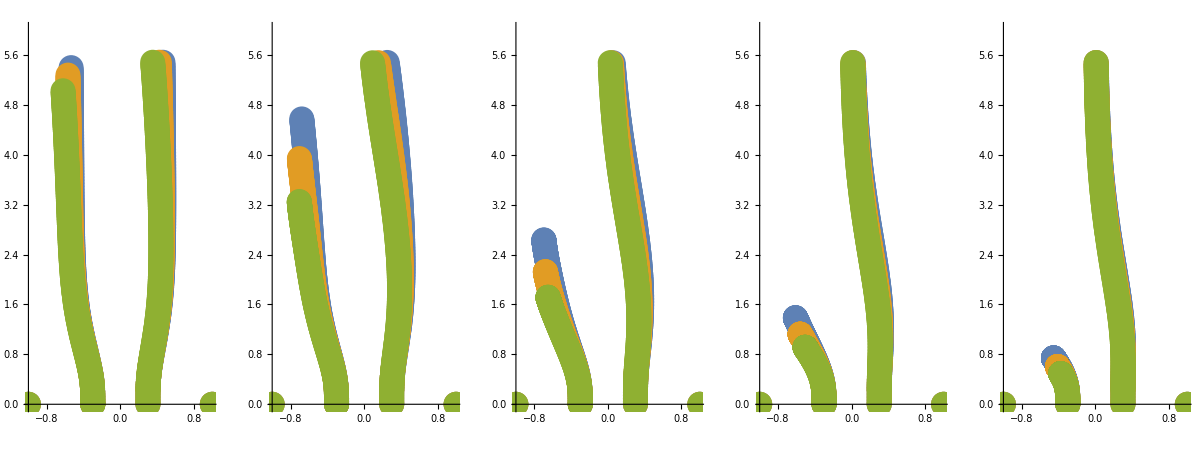
```mathematica
riversim2=-Graphics-
```

#### initialLength5 (riversim with const dt)

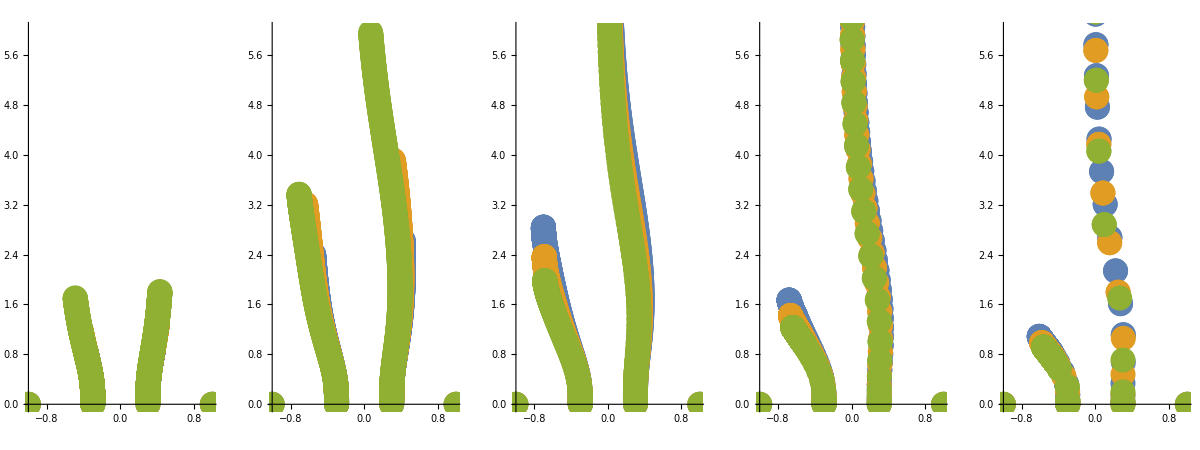
```mathematica
riversim=-Graphics-
```

#### bifurcatedTip (length2 = 0.03)

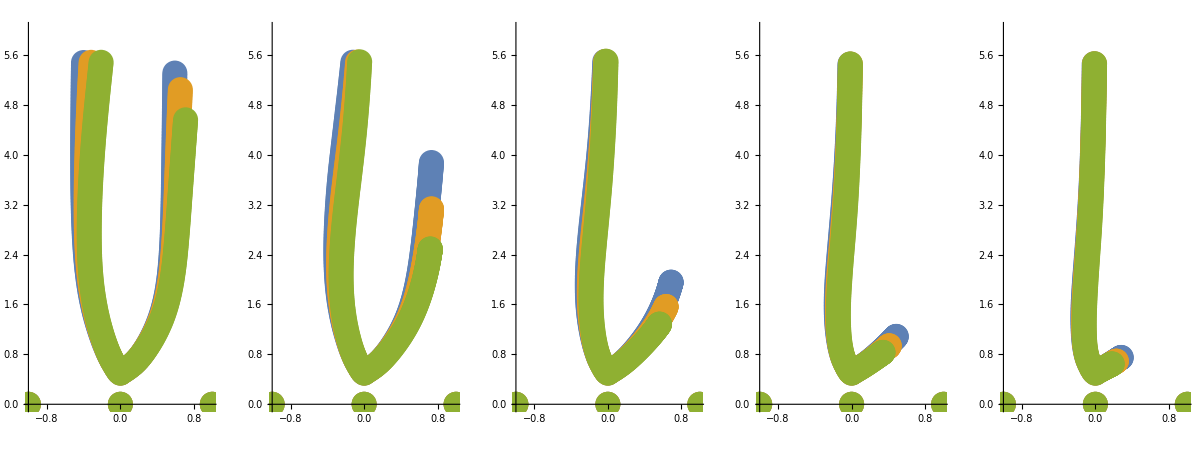

#### initialLength5 (x = 0.3, y = 0.04)

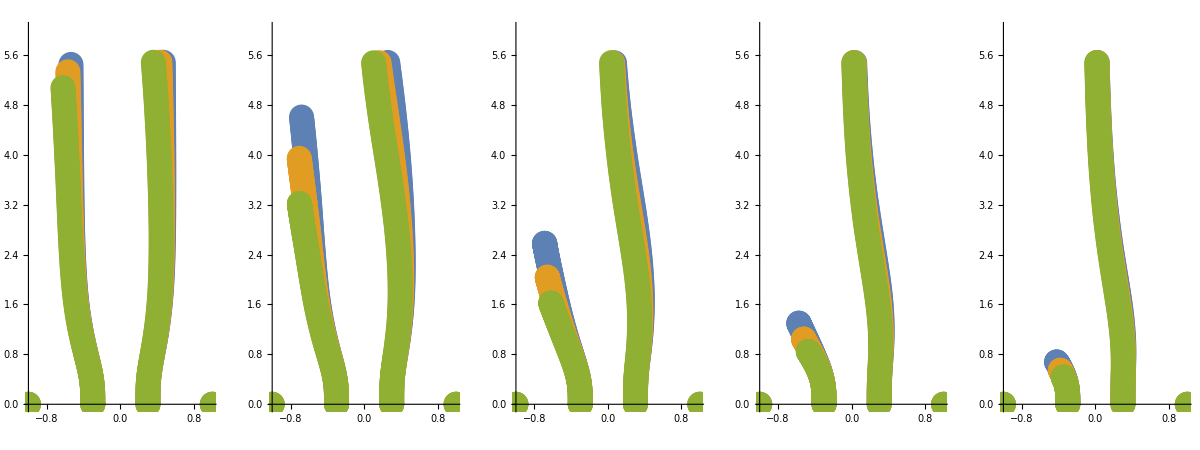
```mathematica
initialLength5=-Graphics-;
```

#### initialLength4 (x = 0.25, y = 0.03)

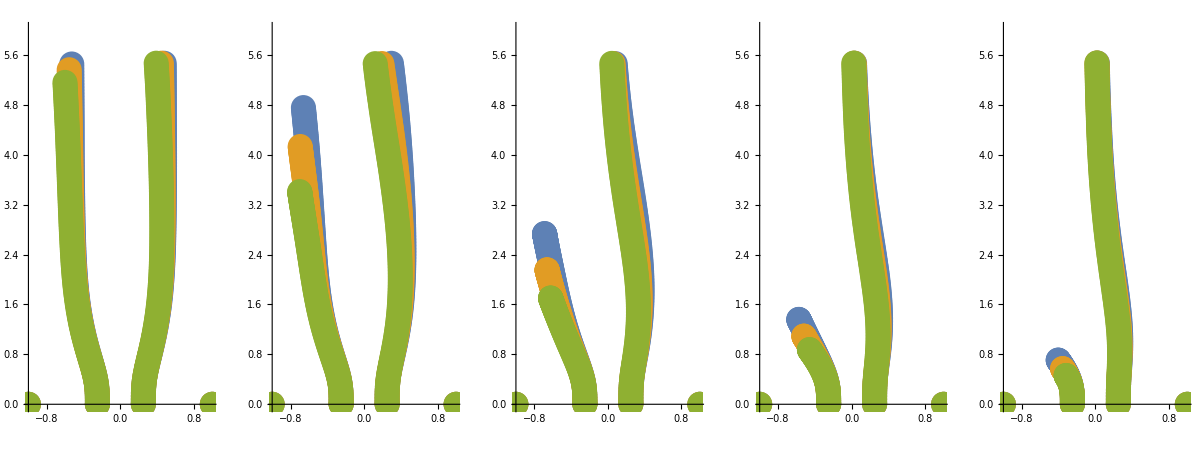
```mathematica
initialLength4=-Graphics-;
```

#### initialLength(x = 0.2, y = 0.1)

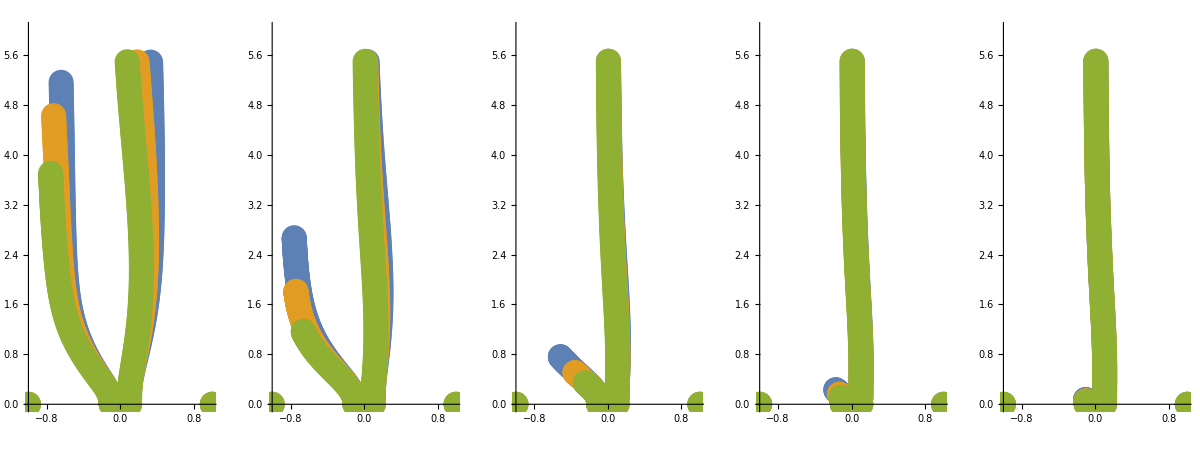
```mathematica
initialLength=-Graphics-;
```

#### initialLength3 (x = 0.25, y = 0.05)

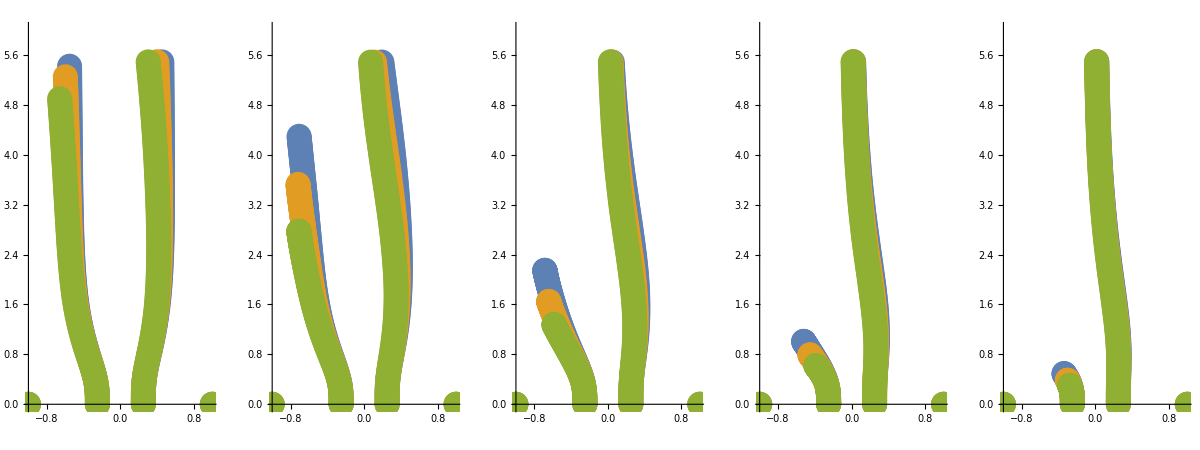
```mathematica
initialLength3=-Graphics-;
```

#### initialLength1(x=0.2,y=0.1)

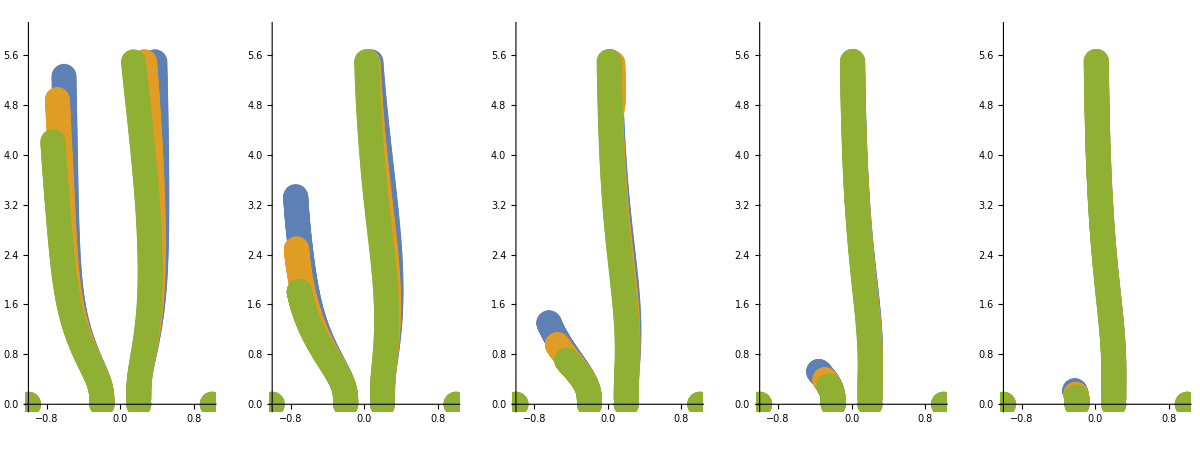
```mathematica
initialLength1=-Graphics-;
```

#### initialLength2(x=0.15,y=0.05)

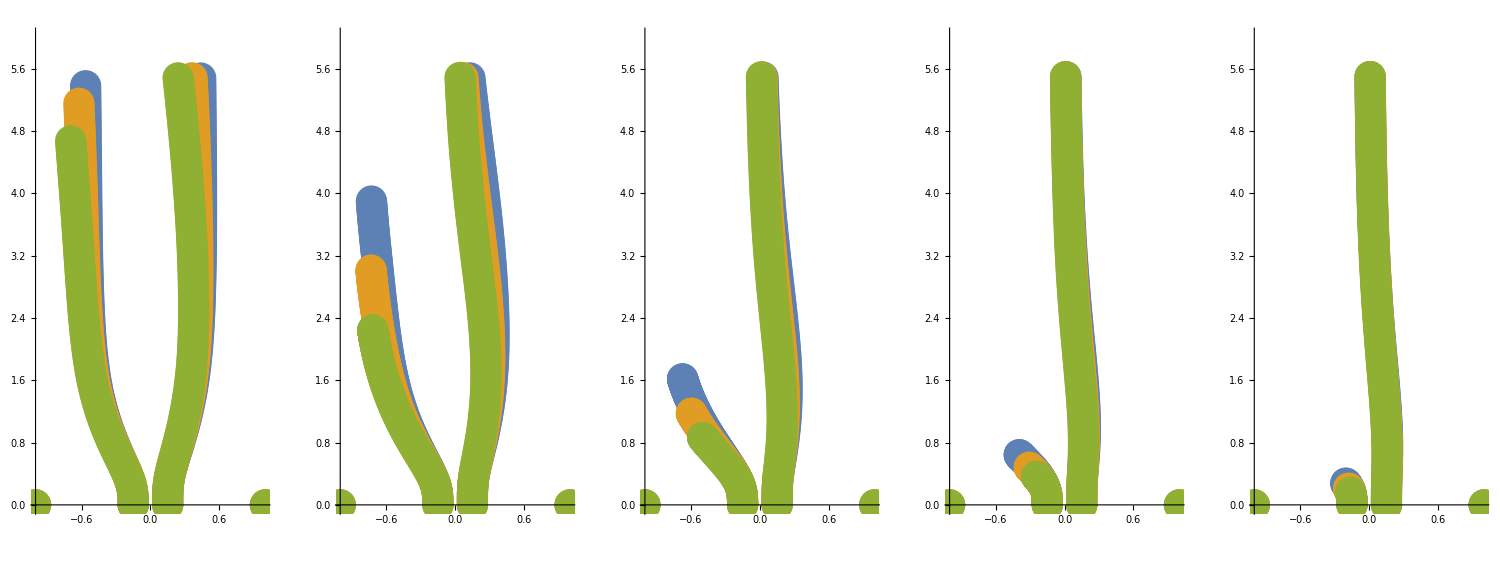
```mathematica
initialLength2=-Graphics-;
```

#### gubiecAsymmetry

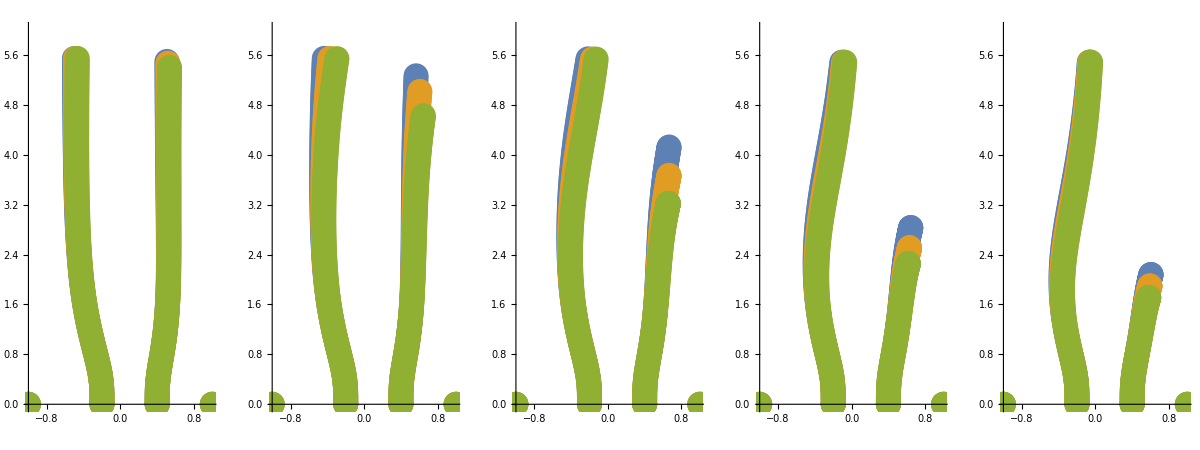
```mathematica
gubiecAsymmetry=-Graphics-;
```

#### gubiecAsymmetry1

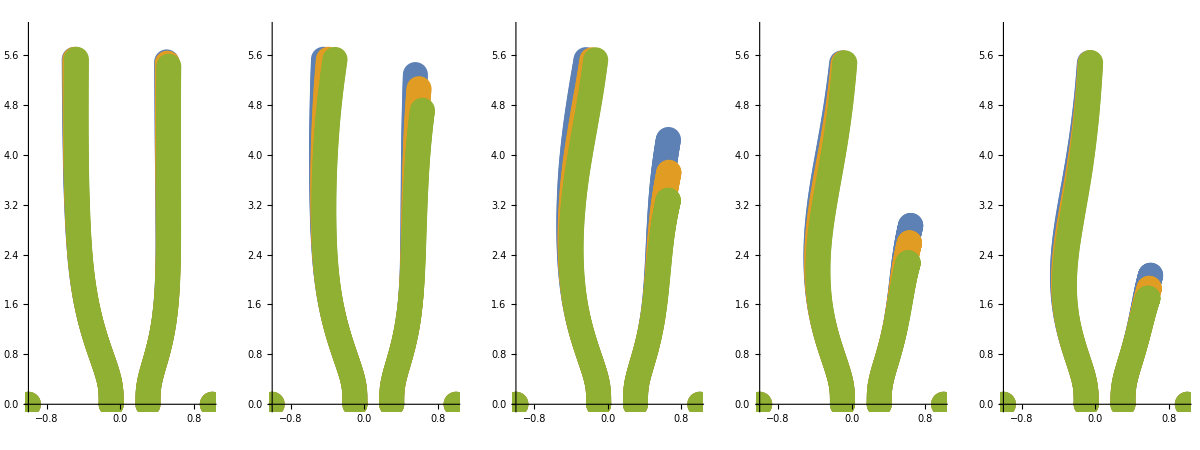
```mathematica
gubiecAsymmetry1=-Graphics-;
```

#### gubiecAsymmetry2

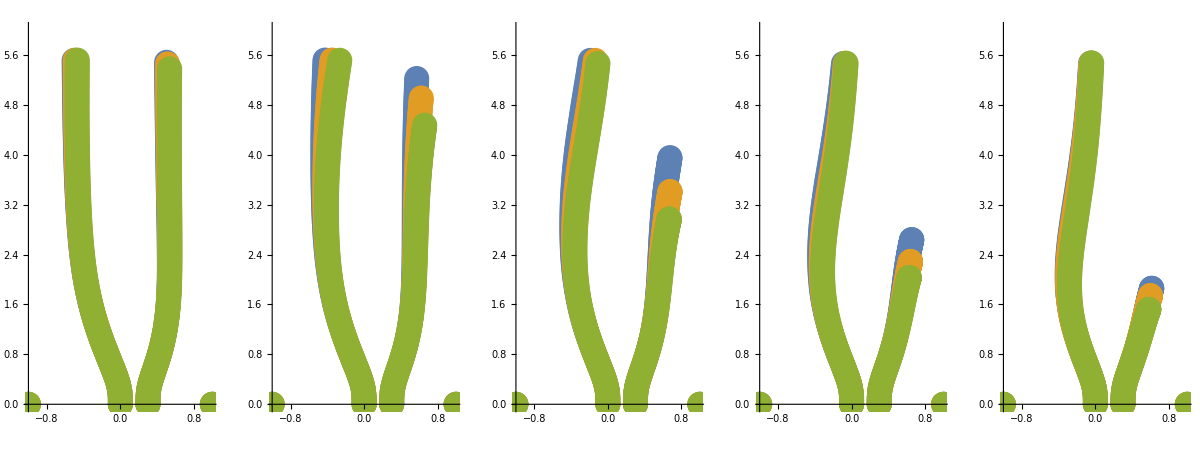
```mathematica
gubiecAsymmetry2=-Graphics-;
```

### Comparison3

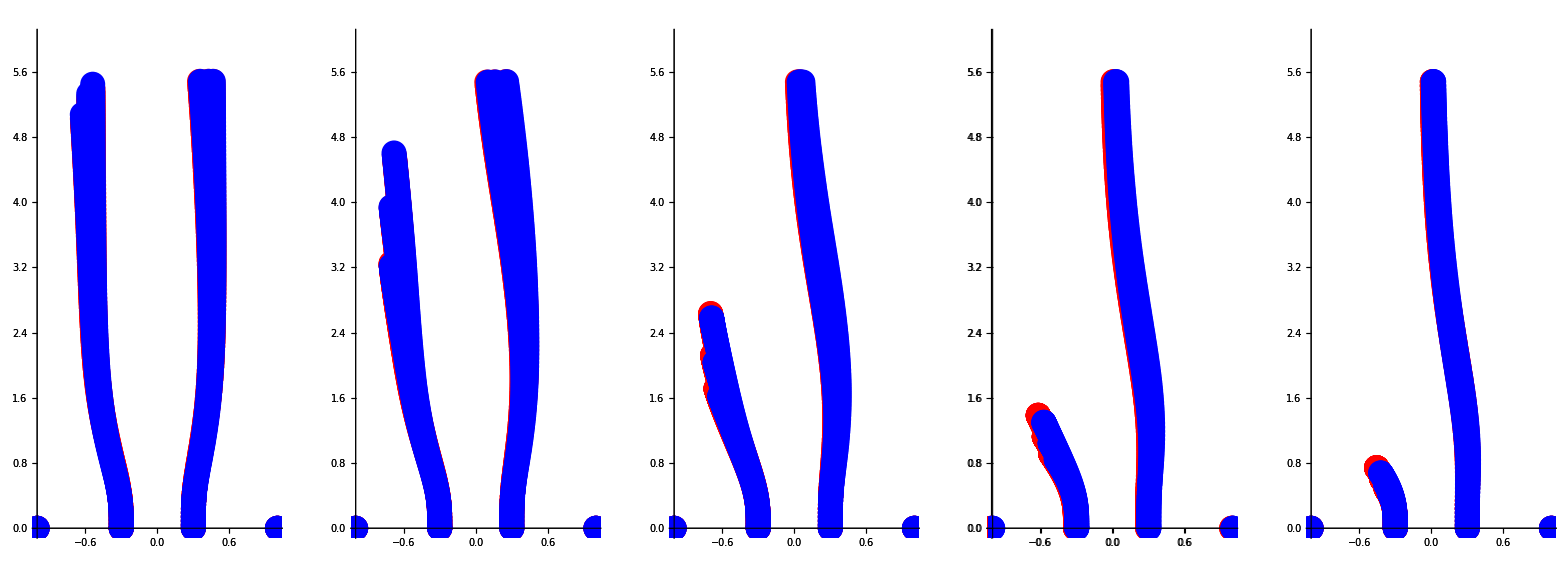
```mathematica
riversimANDmatlabComparison=-Graphics-
```

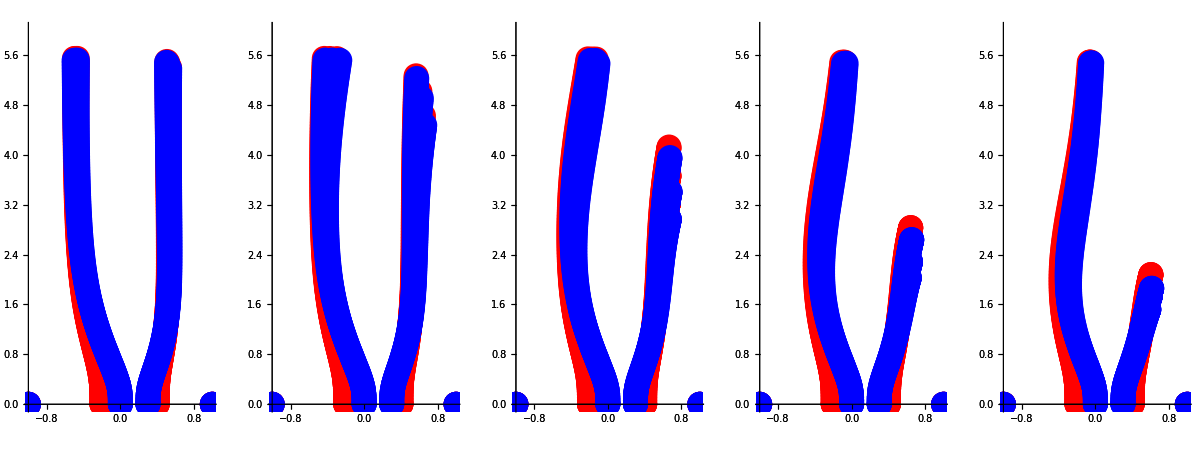

```mathematica
Show[{gubiecAsymmetry/.RGBColor[___]->Red,gubiecAsymmetry2/.RGBColor[___]->Blue}]
```

```mathematica
initialLength5
```

-Graphics-

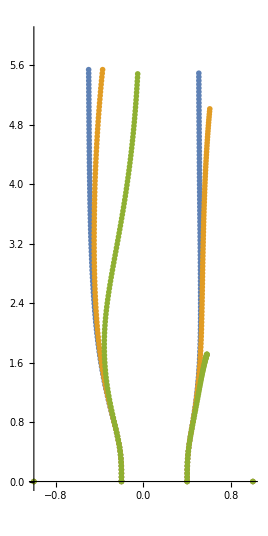

```mathematica
ListPlot[pointsFromMesh/@{1,5,15},PlotStyle->{PointSize->ps},ImageSize->is,PlotRange->pr,AspectRatio->ar,AxesOrigin->{-1,0}]
```

## SINGLE MESH FILE

```mathematica
SetDirectory[NotebookDirectory[]];
data1=Import["previous_dX/lap8.msh","table"];
data2=Import["dX0/lap8.msh","table"];
```

```mathematica
coordsFromGraph={{0.2386363636363636,0.5330578512396695},{0.2923553719008264,0.4896694214876034}};
pr={{coordsFromGraph[[1]][[1]],coordsFromGraph[[2]][[1]]},{coordsFromGraph[[2]][[2]],coordsFromGraph[[1]][[2]]}};
```

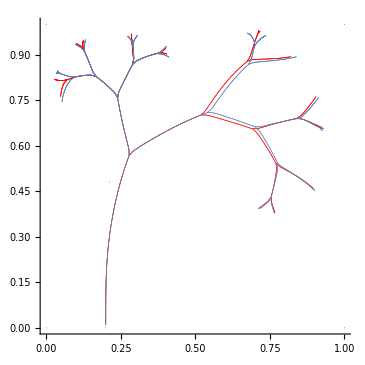

```mathematica
pr={{0,1},{0,1}};
ar=1;
ps=0.001;
subtract=0;
plotGraph[mesh_]:=ListPlot[{mesh[[2;;mesh[[1]][[1]],1;;2]]},PlotStyle->{PointSize->ps},ImageSize->500,PlotRange->pr,AspectRatio->ar,AxesOrigin->{-1,0}];
pointsFromMesh[i_]:=data1[[i]][[2;;data1[[i]][[1]][[1]],1;;2]];
Show[plotGraph@data1/.RGBColor[___]->Red,plotGraph@data2]
```